## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = False;
removeOutputFiles = False;

rxnName="PGMd";
fitLabel="new_lma_Keq_1";
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = True; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)

(* user will need to change this path *)
pathMASSef = "/home/mrama/Desktop/MASSef/";
kineticDataFileName =  "kinetic_data_MASSef.csv";

mainFolder = "fit_PGMd_Keq";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:/home/mrama/Dropbox/MASSef/examples/PGMd/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological];
```

{3pg,Null,Keq substrate}

{0.189,Keq value}

{3pg,Km or S05 substrate}

{0.0002,Km or S05 value}

{2pg,Km or S05 substrate}

{0.00019,Km or S05 value}

{{{3pg,Null},{23dpg,0.0001}},kcat substrates}

{330,kcat value}

{{{2pg,Null},{23dpg,0.0001}},kcat substrates}

{220,kcat value}

((3pg)^c⇌(2pg)^c)^PGMd

;

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg,Null | 0.189 | 0.17955
0.19845 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg | 0.0002 | 0.000173
0.000227 | 23dpg | 0.0001 | M | 7 | 30 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02
1 | 2pg | 0.00019 | 0.000155
0.000225 | 23dpg | 0.0001 | M | 7 | 30 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg | Null
23dpg | 0.0001 | 626.718 | 605.827
647.608 | 1/s | 7 | 37 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02
1 | 2pg | Null
23dpg | 0.0001 | 417.812 | 393.123
442.501 | 1/s | 7 | 37 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority (optional)

```mathematica
(626.7176791692085*0.00019)/(417.8117861128057*0.0002)
KeqList0[[1]][[3]]=1.425; (*kcat_f*km_r / kcat_r*km_f*)
```

1.425

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)


KeqPriorities = {1};
kmPriorities = {1,1};
s05Priorities = Null;
kcatPriorities = {1,1};
inhibitionPriorities=Null;
activationPriorities = Null;
otherParamsPriorities = Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

((3pg)^c⇌(2pg)^c)^PGMd

;

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg,Null | 1.425 | 0.17955
0.19845 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg | 0.0002 | 0.000173
0.000227 | 23dpg | 0.0001 | M | 7 | 30 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02
1 | 2pg | 0.00019 | 0.000155
0.000225 | 23dpg | 0.0001 | M | 7 | 30 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg | Null
23dpg | 0.0001 | 626.718 | 605.827
647.608 | 1/s | 7 | 37 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02
1 | 2pg | Null
23dpg | 0.0001 | 417.812 | 393.123
442.501 | 1/s | 7 | 37 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
catalyticBranch={"E_PGMd[c] + 23dpg[c] <=> E_PGMd[c]&23dpg",
				"E_PGMd[c]&23dpg + 3pg[c] <=> E_PGMd[c]&23dpg&3pg",
				"E_PGMd[c]&23dpg&3pg <=> E_PGMd[c]&23dpg&2pg",
				"E_PGMd[c]&23dpg&2pg <=> E_PGMd[c]&23dpg + 2pg[c]"};

enzymeModelOrig=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModelOrig["Reactions"]
```

{((PGMd^c)_^+(23dpg)^c⇌(PGMd^c&(23dpg)^c)_^)^PGMd1,((PGMd^c&(23dpg)^c)_^+(3pg)^c⇌(PGMd^c&(23dpg)^c&(3pg)^c)_^)^PGMd2,((PGMd^c&(23dpg)^c&(2pg)^c)_^⇌(PGMd^c&(23dpg)^c)_^+(2pg)^c)^PGMd3,((PGMd^c&(23dpg)^c&(3pg)^c)_^⇌(PGMd^c&(23dpg)^c&(2pg)^c)_^)^PGMd4}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((PGMd^c&(23dpg)^c)_^+(3pg)^c⇌(PGMd^c&(23dpg)^c&(3pg)^c)_^)^PGMd2,Overscript[(PGMd^c&(23dpg)^c&(2pg)^c)_^⇌(PGMd^c&(23dpg)^c)_^+(2pg)^c, PGMd3],((PGMd^c&(23dpg)^c&(3pg)^c)_^⇌(PGMd^c&(23dpg)^c&(2pg)^c)_^)^PGMd4};
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

## Set up rate equations

```mathematica
Get["MASSef`"];
```

```mathematica
deleteDirectoryContents[inputPath];
```

```mathematica
MWCFlag=False;
nActiveSites=1;
assumedSaturatingConc = 1;
simplifyFlag=True;
simplifyMaxTime=30;
otherMetsReverseZeroSub={};
 otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModelOrig, rxn, rxnName, inputPath, {},{}, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites, assumedSaturatingConc];
```

{(3pg)^c→0}

{(2pg)^c→0}

{(3pg)^c→1}

{(2pg)^c→1}

{}

Added inhibition reactions:

{}

Generating flux equation...

{((PGMd^c&(23dpg)^c&(3pg)^c)_^-((PGMd^c&(23dpg)^c&(2pg)^c)_^)/K_PGMd4) Volume_c k_PGMd4^⟶}

Volume_c (-(PGMd^c&(23dpg)^c&(2pg)^c)_^ k_PGMd4^⟵+(PGMd^c&(23dpg)^c&(3pg)^c)_^ k_PGMd4^⟶)

1

2

3

0.03414

4

0.00028

5

0.000077

Simplifying...

6

0.048904

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

```mathematica
enzymeModel["Reactions"]
```

{((PGMd^c)_^+(23dpg)^c⇌(PGMd^c&(23dpg)^c)_^)^PGMd1,((PGMd^c&(23dpg)^c)_^+(3pg)^c⇌(PGMd^c&(23dpg)^c&(3pg)^c)_^)^PGMd2,((PGMd^c&(23dpg)^c&(2pg)^c)_^⇌(PGMd^c&(23dpg)^c)_^+(2pg)^c)^PGMd3,((PGMd^c&(23dpg)^c&(3pg)^c)_^⇌(PGMd^c&(23dpg)^c&(2pg)^c)_^)^PGMd4}

## Simulate Data

```mathematica
customRatiosDataList={};
```

### Simulate data without uncertainty

```mathematica
fitLabel
```

new_lma_Keq_1

```mathematica
fitLabel="new_lma_Keq_3";
```

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

```mathematica
FilePrint@dataPathList
```

Priority	23dpg[c]	2pg[c]	3pg[c]	param_PGMd_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd_Keq/input/haldaneRatio_1.txt"	1.425
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd_Keq/input/haldaneRatio_1.txt"	1.425
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd_Keq/input/haldaneRatio_1.txt"	1.425
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd_Keq/input/haldaneRatio_1.txt"	1.425
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd_Keq/input/haldaneRatio_1.txt"	1.425
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd_Keq/input/haldaneRatio_1.txt"	1.425
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd_Keq/input/haldaneRatio_1.txt"	1.425
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd_Keq/input/haldaneRatio_1.txt"	1.425
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd_Keq/input/haldaneRatio_1.txt"	1.425
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd_Keq/input/haldaneRatio_1.txt"	1.425
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd_Keq/input/haldaneRatio_1.txt"	1.425
1	0.0001	0	0.00002	1	7	30	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd_Keq/input/relRateFor_3pg.txt"	0.09090909090909091
1	0.0001	0	0.00003169786384922229	1	7	30	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd_Keq/input/relRateFor_3pg.txt"	0.13680688860321008
1	0.0001	0	0.00005023772863019165	1	7	30	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd_Keq/input/relRateFor_3pg.txt"	0.2007600089131019
1	0.0001	0	0.00007962143411069939	1	7	30	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd_Keq/input/relRateFor_3pg.txt"	0.2847472489508013
1	0.0001	0	0.0001261914688960386	1	7	30	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd_Keq/input/relRateFor_3pg.txt"	0.38686317984685686
1	0.0001	0	0.00020000000000000004	1	7	30	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd_Keq/input/relRateFor_3pg.txt"	0.5
1	0.0001	0	0.0003169786384922229	1	7	30	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd_Keq/input/relRateFor_3pg.txt"	0.6131368201531432
1	0.0001	0	0.0005023772863019165	1	7	30	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd_Keq/input/relRateFor_3pg.txt"	0.7152527510491988
1	0.0001	0	0.0007962143411069948	1	7	30	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd_Keq/input/relRateFor_3pg.txt"	0.7992399910868982
1	0.0001	0	0.0012619146889603862	1	7	30	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd_Keq/input/relRateFor_3pg.txt"	0.8631931113967899
1	0.0001	0	0.0020000000000000005	1	7	30	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd_Keq/input/relRateFor_3pg.txt"	0.9090909090909091
1	0.0001	0.000018999999999999994	0	1	7	30	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd_Keq/input/relRateRev_2pg.txt"	0.09090909090909087
1	0.0001	0.00003011297065676116	0	1	7	30	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd_Keq/input/relRateRev_2pg.txt"	0.13680688860321003
1	0.0001	0.00004772584219868205	0	1	7	30	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd_Keq/input/relRateRev_2pg.txt"	0.20076000891310186
1	0.0001	0.0000756403624051644	0	1	7	30	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd_Keq/input/relRateRev_2pg.txt"	0.2847472489508012
1	0.0001	0.00011988189545123664	0	1	7	30	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd_Keq/input/relRateRev_2pg.txt"	0.38686317984685686
1	0.0001	0.00018999999999999996	0	1	7	30	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd_Keq/input/relRateRev_2pg.txt"	0.49999999999999994
1	0.0001	0.0003011297065676116	0	1	7	30	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd_Keq/input/relRateRev_2pg.txt"	0.6131368201531432
1	0.0001	0.0004772584219868205	0	1	7	30	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd_Keq/input/relRateRev_2pg.txt"	0.7152527510491987
1	0.0001	0.0007564036240516448	0	1	7	30	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd_Keq/input/relRateRev_2pg.txt"	0.7992399910868982
1	0.0001	0.0011988189545123664	0	1	7	30	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd_Keq/input/relRateRev_2pg.txt"	0.8631931113967899
1	0.0001	0.0018999999999999996	0	1	7	30	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd_Keq/input/relRateRev_2pg.txt"	0.9090909090909092
1	0.0001	0	1	1	7	37	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd_Keq/input/absRateFor.txt"	626.7176791692085
1	0.0001	0	1	1	7	37	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd_Keq/input/absRateFor.txt"	626.7176791692085
1	0.0001	0	1	1	7	37	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd_Keq/input/absRateFor.txt"	626.7176791692085
1	0.0001	0	1	1	7	37	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd_Keq/input/absRateFor.txt"	626.7176791692085
1	0.0001	0	1	1	7	37	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd_Keq/input/absRateFor.txt"	626.7176791692085
1	0.0001	0	1	1	7	37	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd_Keq/input/absRateFor.txt"	626.7176791692085
1	0.0001	0	1	1	7	37	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd_Keq/input/absRateFor.txt"	626.7176791692085
1	0.0001	0	1	1	7	37	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd_Keq/input/absRateFor.txt"	626.7176791692085
1	0.0001	0	1	1	7	37	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd_Keq/input/absRateFor.txt"	626.7176791692085
1	0.0001	0	1	1	7	37	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd_Keq/input/absRateFor.txt"	626.7176791692085
1	0.0001	0	1	1	7	37	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd_Keq/input/absRateFor.txt"	626.7176791692085
1	0.0001	1	0	1	7	37	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd_Keq/input/absRateRev.txt"	417.8117861128057
1	0.0001	1	0	1	7	37	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd_Keq/input/absRateRev.txt"	417.8117861128057
1	0.0001	1	0	1	7	37	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd_Keq/input/absRateRev.txt"	417.8117861128057
1	0.0001	1	0	1	7	37	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd_Keq/input/absRateRev.txt"	417.8117861128057
1	0.0001	1	0	1	7	37	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd_Keq/input/absRateRev.txt"	417.8117861128057
1	0.0001	1	0	1	7	37	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd_Keq/input/absRateRev.txt"	417.8117861128057
1	0.0001	1	0	1	7	37	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd_Keq/input/absRateRev.txt"	417.8117861128057
1	0.0001	1	0	1	7	37	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd_Keq/input/absRateRev.txt"	417.8117861128057
1	0.0001	1	0	1	7	37	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd_Keq/input/absRateRev.txt"	417.8117861128057
1	0.0001	1	0	1	7	37	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd_Keq/input/absRateRev.txt"	417.8117861128057
1	0.0001	1	0	1	7	37	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd_Keq/input/absRateRev.txt"	417.8117861128057

### Simulate data with uncertainty

```mathematica
nSamples=3;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList];
```

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

```mathematica
FilePrint[dataPathList[[1]]]
```

dhap[c]	g3p[c]	param_TPI_total	param_pH	param_Temp	FileFlag	Target_Data
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0.00008706103516902622	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.09090909090909086
0	0.00013798244196800728	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.13680688860320997
0	0.00021868743295425528	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.20076000891310164
0	0.0003465962237659955	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.28474724895080133
0	0.0005493179955794547	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.38686317984685675
0	0.0008706103516902622	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.49999999999999983
0	0.001379824419680073	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.6131368201531431
0	0.002186874329542555	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.7152527510491986
0	0.003465962237659955	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.7992399910868982
0	0.005493179955794547	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.8631931113967899
0	0.008706103516902621	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.909090909090909
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051

### Parameter scan

```mathematica
Export["TPIParameterScanArguments.mx",{paramScanList, enzymeModel, dataFileName, 
						  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList}, "MX"];

Export["TPIParameterScanResults.mx",{allFittingDataList, dataPathList, fileList, fileListSub},"MX"];
```

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"kcat",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, fitLabel,
						  haldaneRatiosList, KeqList,
 kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

```mathematica
FilePrint[dataPathList[[5]]]
```

dhap[c]	g3p[c]	param_TPI_total	param_pH	param_Temp	FileFlag	Target_Data
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0.00010299999999999996	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.09090909090909087
0	0.00016324399882349468	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.13680688860321
0	0.00025872430244548657	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.20076000891310164
0	0.00041005038567010205	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.28474724895080133
0	0.0006498860648145985	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.3868631798468567
0	0.0010299999999999994	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.4999999999999999
0	0.0016324399882349469	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.613136820153143
0	0.0025872430244548686	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.7152527510491986
0	0.004100503856701021	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.7992399910868982
0	0.006498860648145985	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.8631931113967899
0	0.010299999999999995	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.9090909090909091
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numTrials=100;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numTrials,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numTrials, dataPathList]
```

best_fit: 0.955445303646
best_fit: 0.954871390608
best_fit: 0.558313222526
best_fit: 0.727141762886
best_fit: 1.07227193736
best_fit: 0.536641547458
best_fit: 0.893184778237
best_fit: 0.352356062997
best_fit: 1.07923387486
best_fit: 0.836260225354
best_fit: 0.728480672559
best_fit: 1.09920119229
best_fit: 0.812473098237
best_fit: 1.098810481
best_fit: 0.654416848084
best_fit: 1.07771968631
best_fit: 0.671047448879
best_fit: 0.984477320804
best_fit: 1.09803744856
best_fit: 1.03686721757
best_fit: 0.16424736792
best_fit: 1.03566995163
best_fit: 0.823006126358
best_fit: 0.987153986173
best_fit: 1.09327090449
best_fit: 1.00607753414
best_fit: 0.801573796445
best_fit: 0.813823602012
best_fit: 0.757732214169
best_fit: 1.0407471427
best_fit: 1.07762617424
best_fit: 0.852340961761
best_fit: 0.964951368156
best_fit: 0.187902279576
best_fit: 0.843203932175
best_fit: 1.04758725725
best_fit: 1.0028584089
best_fit: 0.945798543089
best_fit: 0.312694761593
best_fit: 0.850039981032
best_fit: 0.625272451354
best_fit: 0.547078038927
best_fit: 0.84638060921
best_fit: 0.993520962451
best_fit: 1.05272992239
best_fit: 0.955437903093
best_fit: 0.976887340586
best_fit: 0.63269368479
best_fit: 1.08419756203
best_fit: 0.566963420012
best_fit: 0.788635008817
best_fit: 0.886078630853
best_fit: 0.475953315451
best_fit: 1.07841411503
best_fit: 1.07541481937
best_fit: 1.05462213412
best_fit: 1.04407749
best_fit: 0.61298336533
best_fit: 0.678014409031
best_fit: 0.830162513892
best_fit: 1.084774166
best_fit: 0.970651928326
best_fit: 0.659203676966
best_fit: 0.838183746034
best_fit: 1.04620714584
best_fit: 0.533392109523
best_fit: 1.0910509745
best_fit: 1.01650986878
best_fit: 0.960601467932
best_fit: 0.351382507616
best_fit: 0.305865101548
best_fit: 1.09970463767
best_fit: 0.916357771694
best_fit: 0.840325753902
best_fit: 0.638836777344
best_fit: 1.04496871033
best_fit: 0.675031866935
best_fit: 0.88301558736
best_fit: 0.659788823532
best_fit: 0.506896843149
best_fit: 0.876653681637
best_fit: 0.828882161394
best_fit: 1.08720320521
best_fit: 1.08494596383
best_fit: 0.874189385562
best_fit: 0.600025453919
best_fit: 0.802887029357
best_fit: 1.06173992935
best_fit: 1.08983259363
best_fit: 1.0114953699
best_fit: 0.593276812457
best_fit: 1.06509462237
best_fit: 0.549664417759
best_fit: 1.02720643919
best_fit: 0.382307792974
best_fit: 1.00502921081
best_fit: 1.08490643834
best_fit: 0.672167888594
best_fit: 0.755563662339
best_fit: 1.00608408479

## Evaluate fit results

```mathematica
(*no uncertainty or parameter scan*)
lmaResultsFileNameNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(*with uncertainty or parameter scan*)
datasetI=2;
lmaResultsFileNameNew=StringTake[lmaResultsFileName,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

StringTake::strse: String or list of strings expected at position 1 in StringTake[lmaResultsFileName,1;;-5].

StringJoin::string: String expected at position 1 in StringTake[lmaResultsFileName,1;;-5]<>_2.txt.

Part::partd: Part specification /home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test_kcatKm_defs/input/TPI_general.dat⟦2⟧ is longer than depth of object.

```mathematica
dataFilePath
```

/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd/input/PGMd_new_lma_1.dat

```mathematica
flagFitType = "log_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNameNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, fitLabel<>"_"<>flagFitType];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 2.44295×10^-7 | 5.96798×10^-14 | 8.01575×10^-7 | 0.0000562509 | 1.425 | 1.425
1 | haldaneRatio_1 | 2.44295×10^-7 | 5.96798×10^-14 | 8.01575×10^-7 | 0.0000562509 | 1.425 | 1.425
1 | haldaneRatio_1 | 2.44295×10^-7 | 5.96798×10^-14 | 8.01575×10^-7 | 0.0000562509 | 1.425 | 1.425
1 | haldaneRatio_1 | 2.44295×10^-7 | 5.96798×10^-14 | 8.01575×10^-7 | 0.0000562509 | 1.425 | 1.425
1 | haldaneRatio_1 | 2.44295×10^-7 | 5.96798×10^-14 | 8.01575×10^-7 | 0.0000562509 | 1.425 | 1.425
1 | haldaneRatio_1 | 2.44295×10^-7 | 5.96798×10^-14 | 8.01575×10^-7 | 0.0000562509 | 1.425 | 1.425
1 | haldaneRatio_1 | 2.44295×10^-7 | 5.96798×10^-14 | 8.01575×10^-7 | 0.0000562509 | 1.425 | 1.425
1 | haldaneRatio_1 | 2.44295×10^-7 | 5.96798×10^-14 | 8.01575×10^-7 | 0.0000562509 | 1.425 | 1.425
1 | haldaneRatio_1 | 2.44295×10^-7 | 5.96798×10^-14 | 8.01575×10^-7 | 0.0000562509 | 1.425 | 1.425
1 | haldaneRatio_1 | 2.44295×10^-7 | 5.96798×10^-14 | 8.01575×10^-7 | 0.0000562509 | 1.425 | 1.425
1 | haldaneRatio_1 | 2.44295×10^-7 | 5.96798×10^-14 | 8.01575×10^-7 | 0.0000562509 | 1.425 | 1.425
1 | relRateFor_3pg | 0.0000315839 | 9.97542×10^-10 | 6.61109×10^-6 | 0.0072722 | 0.0909091 | 0.0909025
1 | relRateFor_3pg | 0.0000256039 | 6.5556×10^-10 | 8.06523×10^-6 | 0.00589534 | 0.136807 | 0.136799
1 | relRateFor_3pg | 0.0000172714 | 2.983×10^-10 | 7.98382×10^-6 | 0.0039768 | 0.20076 | 0.200752
1 | relRateFor_3pg | 6.32829×10^-6 | 4.00473×10^-11 | 4.14915×10^-6 | 0.00145713 | 0.284747 | 0.284743
1 | relRateFor_3pg | 6.97721×10^-6 | 4.86814×10^-11 | 6.21524×10^-6 | 0.00160657 | 0.386863 | 0.386869
1 | relRateFor_3pg | 0.0000217192 | 4.71723×10^-10 | 0.0000250058 | 0.00500115 | 0.5 | 0.500025
1 | relRateFor_3pg | 0.0000364617 | 1.32945×10^-9 | 0.0000514787 | 0.00839596 | 0.613137 | 0.613188
1 | relRateFor_3pg | 0.0000497685 | 2.4769×10^-9 | 0.0000819699 | 0.0114603 | 0.715253 | 0.715335
1 | relRateFor_3pg | 0.0000607132 | 3.6861×10^-9 | 0.000111739 | 0.0139807 | 0.79924 | 0.799352
1 | relRateFor_3pg | 0.0000690474 | 4.76755×10^-9 | 0.000137248 | 0.0159 | 0.863193 | 0.86333
1 | relRateFor_3pg | 0.0000750288 | 5.62932×10^-9 | 0.000157068 | 0.0172775 | 0.909091 | 0.909248
1 | relRateRev_2pg | 0.0000313124 | 9.80469×10^-10 | 6.55427×10^-6 | 0.0072097 | 0.0909091 | 0.0909025
1 | relRateRev_2pg | 0.0000255654 | 6.53591×10^-10 | 8.05312×10^-6 | 0.00588648 | 0.136807 | 0.136799
1 | relRateRev_2pg | 0.0000175575 | 3.08267×10^-10 | 8.1161×10^-6 | 0.00404269 | 0.20076 | 0.200752
1 | relRateRev_2pg | 7.04083×10^-6 | 4.95732×10^-11 | 4.61631×10^-6 | 0.0016212 | 0.284747 | 0.284743
1 | relRateRev_2pg | 5.74625×10^-6 | 3.30194×10^-11 | 5.11871×10^-6 | 0.00132313 | 0.386863 | 0.386868
1 | relRateRev_2pg | 0.0000199138 | 3.9656×10^-10 | 0.0000229272 | 0.00458543 | 0.5 | 0.500023
1 | relRateRev_2pg | 0.0000340819 | 1.16157×10^-9 | 0.0000481186 | 0.00784794 | 0.613137 | 0.613185
1 | relRateRev_2pg | 0.0000468701 | 2.19681×10^-9 | 0.000077196 | 0.0107928 | 0.715253 | 0.71533
1 | relRateRev_2pg | 0.0000573884 | 3.29343×10^-9 | 0.00010562 | 0.013215 | 0.79924 | 0.799346
1 | relRateRev_2pg | 0.0000653978 | 4.27688×10^-9 | 0.000129993 | 0.0150595 | 0.863193 | 0.863323
1 | relRateRev_2pg | 0.0000711461 | 5.06177×10^-9 | 0.000148939 | 0.0163833 | 0.909091 | 0.90924
1 | absRateFor | 2.44402×10^-7 | 5.97321×10^-14 | 0.000352689 | 0.0000562756 | 626.718 | 626.718
1 | absRateFor | 2.44402×10^-7 | 5.97321×10^-14 | 0.000352689 | 0.0000562756 | 626.718 | 626.718
1 | absRateFor | 2.44402×10^-7 | 5.97321×10^-14 | 0.000352689 | 0.0000562756 | 626.718 | 626.718
1 | absRateFor | 2.44402×10^-7 | 5.97321×10^-14 | 0.000352689 | 0.0000562756 | 626.718 | 626.718
1 | absRateFor | 2.44402×10^-7 | 5.97321×10^-14 | 0.000352689 | 0.0000562756 | 626.718 | 626.718
1 | absRateFor | 2.44402×10^-7 | 5.97321×10^-14 | 0.000352689 | 0.0000562756 | 626.718 | 626.718
1 | absRateFor | 2.44402×10^-7 | 5.97321×10^-14 | 0.000352689 | 0.0000562756 | 626.718 | 626.718
1 | absRateFor | 2.44402×10^-7 | 5.97321×10^-14 | 0.000352689 | 0.0000562756 | 626.718 | 626.718
1 | absRateFor | 2.44402×10^-7 | 5.97321×10^-14 | 0.000352689 | 0.0000562756 | 626.718 | 626.718
1 | absRateFor | 2.44402×10^-7 | 5.97321×10^-14 | 0.000352689 | 0.0000562756 | 626.718 | 626.718
1 | absRateFor | 2.44402×10^-7 | 5.97321×10^-14 | 0.000352689 | 0.0000562756 | 626.718 | 626.718
1 | absRateRev | 2.44203×10^-7 | 5.9635×10^-14 | 0.000234934 | 0.0000562297 | 417.812 | 417.812
1 | absRateRev | 2.44203×10^-7 | 5.9635×10^-14 | 0.000234934 | 0.0000562297 | 417.812 | 417.812
1 | absRateRev | 2.44203×10^-7 | 5.9635×10^-14 | 0.000234934 | 0.0000562297 | 417.812 | 417.812
1 | absRateRev | 2.44203×10^-7 | 5.9635×10^-14 | 0.000234934 | 0.0000562297 | 417.812 | 417.812
1 | absRateRev | 2.44203×10^-7 | 5.9635×10^-14 | 0.000234934 | 0.0000562297 | 417.812 | 417.812
1 | absRateRev | 2.44203×10^-7 | 5.9635×10^-14 | 0.000234934 | 0.0000562297 | 417.812 | 417.812
1 | absRateRev | 2.44203×10^-7 | 5.9635×10^-14 | 0.000234934 | 0.0000562297 | 417.812 | 417.812
1 | absRateRev | 2.44203×10^-7 | 5.9635×10^-14 | 0.000234934 | 0.0000562297 | 417.812 | 417.812
1 | absRateRev | 2.44203×10^-7 | 5.9635×10^-14 | 0.000234934 | 0.0000562297 | 417.812 | 417.812
1 | absRateRev | 2.44203×10^-7 | 5.9635×10^-14 | 0.000234934 | 0.0000562297 | 417.812 | 417.812
1 | absRateRev | 2.44203×10^-7 | 5.9635×10^-14 | 0.000234934 | 0.0000562297 | 417.812 | 417.812

### Simulated Data and Best Fit Data Plot

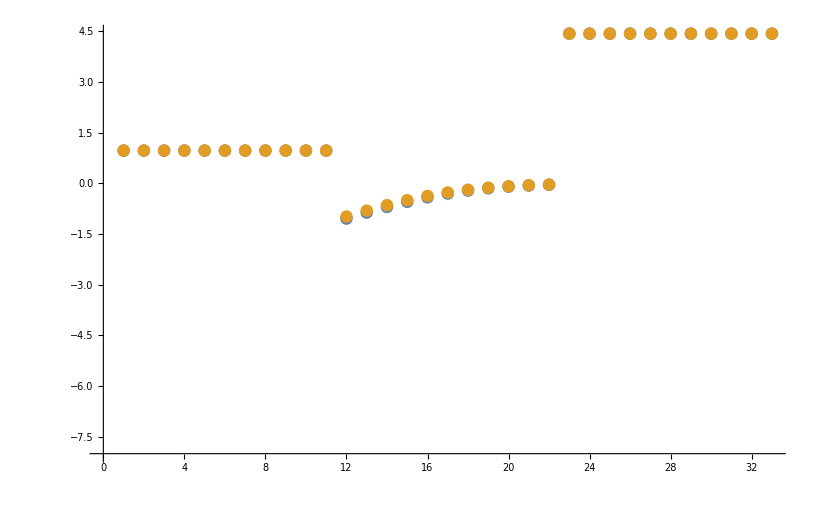

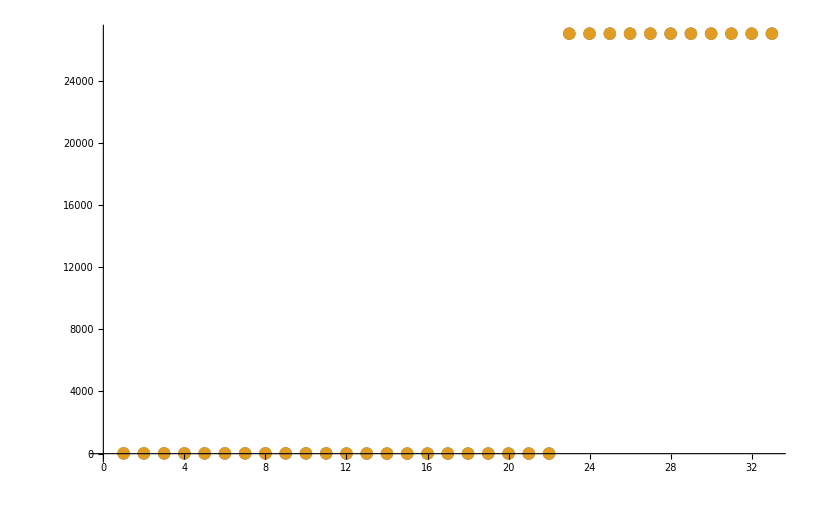

```mathematica
datasetI=40;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[datasetI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[datasetI,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

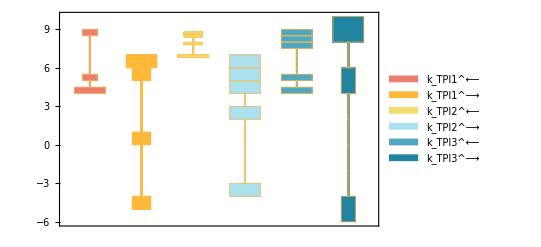

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

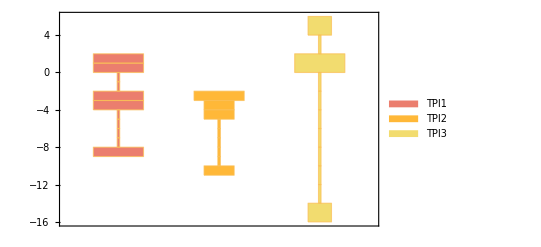

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

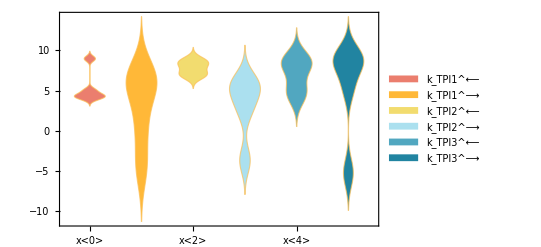

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1
assumedSaturatingConc=1
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[1,2]]]
```

PGMd_total_Global→1

1

{k_PGMd1^⟵→0.0277271,k_PGMd1^⟶→13421.6,k_PGMd2^⟵→298072.,k_PGMd2^⟶→8.90642×10^8,k_PGMd3^⟵→2.4062×10^8,k_PGMd3^⟶→17528.1,k_PGMd4^⟵→512.491,k_PGMd4^⟶→543.873}

```mathematica
backCalculateKmsLocal[rxn, kmList, relativeRateForward, relativeRateReverse, metSatForSub, metSatRevSub,paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

g3p^c

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{g3p^c→(k_TPI1^⟵ k_TPI2^⟶+k_TPI1^⟵ k_TPI3^⟵+k_TPI2^⟶ k_TPI3^⟶)/(2. k_TPI1^⟵ k_TPI2^⟶+k_TPI1^⟶ k_TPI2^⟶+2. k_TPI1^⟵ k_TPI3^⟵+k_TPI1^⟶ k_TPI3^⟵+k_TPI1^⟶ k_TPI3^⟶+2. k_TPI2^⟶ k_TPI3^⟶)}}

{}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{g3p^c→0.00103068}}

data value | predicted value | error in %
0.00103 | 0.00103068 | 0.0658914

```mathematica
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse, metSatForSub, metSatRevSub,paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

data value | predicted value | error in %
0.0002 | 0.000331956 | 65.9778
0.00019 | 0.0000763778 | 59.8011

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
626.718 | 512.789 | 18.1787
417.812 | 510.643 | 22.2183

```mathematica
backCalculateRatios[haldaneRatiosList, KeqList[[1]][[3]],  paramFitSub]//TableForm
```

data value | predicted value | error in %
0.189 | 0.230992 | 22.2182

```mathematica
dhapCoSubKm = {};
dhapCoSubKcat = {dhap^c->1};
relRatedhap=Values@FilterRules[fileListSub,inputPath<>"/relRateRev_dhap.txt"];
absRateRev=Values@FilterRules[fileListSub,inputPath<>"/absRateRev.txt"];
```

```mathematica
backCalulateKmSimple[relRate_,paramFitSub_,coSub_,substrate_]:=Block[{kmPredicted},

  kmPredicted = Solve[(relRate/.paramFitSub/. coSub)==0.5, substrate];
	kmPredicted = Flatten[Values @ kmPredicted];
  kmPredicted = If[Length[kmPredicted] > 1,
					Flatten[Select[kmPredicted, Head[#] === Real && #> 0  &]][[1]],
					kmPredicted
				];
Return[kmPredicted]
];
```

```mathematica
absRateRev
```

{(dhap^c TPI_total_Global k_TPI1^⟵ k_TPI2^⟵ k_TPI3^⟵)/(k_TPI1^⟵ (k_TPI2^⟶+k_TPI3^⟵)+k_TPI2^⟶ k_TPI3^⟶+dhap^c k_TPI2^⟵ (k_TPI1^⟵+k_TPI3^⟵+k_TPI3^⟶))}

```mathematica
relRatedhap
```

{(dhap^c (k_TPI1^⟵ (k_TPI2^⟵+k_TPI2^⟶+k_TPI3^⟵)+k_TPI2^⟶ k_TPI3^⟶+k_TPI2^⟵ (k_TPI3^⟵+k_TPI3^⟶)))/(k_TPI1^⟵ (k_TPI2^⟶+k_TPI3^⟵)+k_TPI2^⟶ k_TPI3^⟶+dhap^c k_TPI2^⟵ (k_TPI1^⟵+k_TPI3^⟵+k_TPI3^⟶))}

#### Export rate back calculated parameter error distribution

```mathematica
kmList
```

{{1,3pg,0.0002,{0.000173,0.000227},{{23dpg,0.0001}},M,7,30,{{trishcl,0.03}},{{mg2,0.005},{so4,0.005},{cl,0.02},{k,0.02}}},{1,2pg,0.00019,{0.000155,0.000225},{{23dpg,0.0001}},M,7,30,{{trishcl,0.03}},{{mg2,0.005},{so4,0.005},{cl,0.02},{k,0.02}}}}

```mathematica
kcatList
```

{{1,{{3pg,Null},{23dpg,0.0001}},626.718,{605.827,647.608},1/s,7,37,{{trishcl,0.03}},{{mg2,0.005},{so4,0.005},{cl,0.02},{k,0.02}}},{1,{{2pg,Null},{23dpg,0.0001}},417.812,{393.123,442.501},1/s,7,37,{{trishcl,0.03}},{{mg2,0.005},{so4,0.005},{cl,0.02},{k,0.02}}}}

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
nRateSets=100;
rateConstList=Import[outputPath<>"/treated_data/rateconst_PGMd_"<>fitLabel<>"_"<>flagFitType<>".csv", "TSV"];

predictedParamsErrorList=Table[

(*paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[rateSetI,2]]];*)
paramFitSub=Thread[rateConstsSub[[All,1]]->rateConstList[[rateSetI,2;;]]];

{rateConstList[[rateSetI,1]],
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse, metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName][[2;;,3]],
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc][[2;;,3]],
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]],  paramFitSub][[2,3]]}//Flatten,

{rateSetI, 1, nRateSets}];

predictedParamsErrorList=Insert[predictedParamsErrorList,{"ssd","Km_3pg","Km_2pg","kcat_f","kcat_r","Keq"} , 1];
predictedParamsErrorList=Insert[predictedParamsErrorList,{0,kmList[[1]][[3]],kmList[[2]][[3]], kcatList[[1]][[3]], kcatList[[2]][[3]],KeqList[[1]][[3]]}  ,2];
Export[outputPath<>"/treated_data/predicted_params_error_distribution_"<>fitLabel<>"_"<>flagFitType<>".csv",predictedParamsErrorList,"CSV"];


predictedParamsList=Table[

(*paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[rateSetI,2]]];*)
paramFitSub=Thread[rateConstsSub[[All,1]]->rateConstList[[rateSetI,2;;]]];

{rateConstList[[rateSetI,1]],
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse, metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName][[2;;,2]],
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc][[2;;,2]],
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]],  paramFitSub][[2,2]]}//Flatten,


{rateSetI, 1, nRateSets}];

predictedParamsList=Insert[predictedParamsList,{"ssd","Km_3pg","Km_2pg","kcat_f","kcat_r","Keq"} , 1];
predictedParamsList=Insert[predictedParamsList,{0,kmList[[1]][[3]],kmList[[2]][[3]], kcatList[[1]][[3]], kcatList[[2]][[3]],KeqList[[1]][[3]]}  ,2];
Export[outputPath<>"/treated_data/predicted_params_distribution_"<>fitLabel<>"_"<>flagFitType<>".csv",predictedParamsList,"CSV"];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

```mathematica
backCalulateKmSimple[relRatedhap,paramFitSub,dhapCoSubKm,dhap^c]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{0.268099}

```mathematica
absRateRev
```

{(dhap^c TPI_total_Global k_TPI1^⟵ k_TPI2^⟵ k_TPI3^⟵)/(k_TPI1^⟵ (k_TPI2^⟶+k_TPI3^⟵)+k_TPI2^⟶ k_TPI3^⟶+dhap^c k_TPI2^⟵ (k_TPI1^⟵+k_TPI3^⟵+k_TPI3^⟶))}

```mathematica
absRateRev /. paramFitSub /. dhapCoSubKcat /. enzymeSub
```

{16.5559}

#### Export rate back calculated parameter distribution

```mathematica
nRateSets=100;
predictedParamsList=Table[

paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[rateSetI,2]]];
{filteredDataList[[rateSetI,1]],
backCalculateKms[rxn, kmList, absoluteRateForward, absoluteRateReverse, paramFitSub, assumedSaturatingConc, rxnName][[2,2]],
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc][[2,2]],
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]],  paramFitSub][[2,2]]}//Flatten,

{rateSetI, 1, nRateSets}];

predictedParamsList=Insert[predictedParamsList,{"ssd","Km_g3p","kcat_f","Keq"} , 1];
predictedParamsList=Insert[predictedParamsList,{"Null",kmList[[1]][[3]],kcatList[[1]][[3]], KeqList[[1]][[3]]}  ,2];
Export[outputPath<>"/treated_data/predicted_params_distribution.csv",predictedParamsList,"CSV"];
```